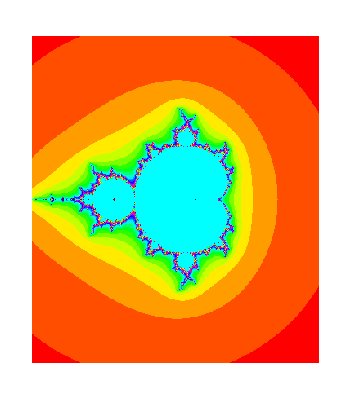

```mathematica
len[x0_,x_,d_]:=Which[Abs[x]>5.,d,Abs[x]<0.01,Infinity,True,If[d<100,1+len[x0,x^2+x0,d+1],0]]
a=Table[Table[len[i+I*j,i+I*j,0],{i,-2,1.5,0.01}],{j,-2,2,0.01}];
ArrayPlot[a,ColorFunction->Function[{x},Hue[x*5]]]
```

-0.825-0.2321 ⅈ

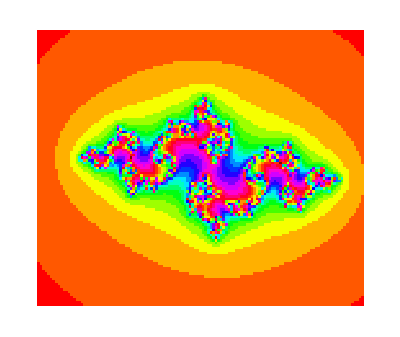

```mathematica
b=-0.825-0.2321I
len[x0_,x_,d_,b_]:=Which[Abs[x]>5.,d,Abs[x]<0.01,Infinity,True,If[d<100,1+len[x0,x^2+b,d+1,b],0]]
a=Table[Table[len[i+I*j,i+I*j,0,b],{i,-2,1.8,0.03}],{j,-1.6,1.6,0.03}];
ArrayPlot[a,ColorFunction->Function[{x},Hue[x*5]]]
```

```mathematica
len[x0_,x_,d_,b_]:=Which[Abs[x]>5.,d,Abs[x]<0.01,Infinity,True,If[d<100,1+len[x0,x^2+b,d+1,b],0]]
anim=Table[ArrayPlot[Table[Table[len[i+I*j,i+I*j,0,-0.825+(k-30)0.01-0.2321+(k-30)0.01 ⅈ],{i,-2,1.8,0.01}],{j,-1.6,1.6,0.01}],ColorFunction->Function[{x},Hue[x*5+k/30]]],{k,50,90,0.2}];
```

```mathematica
Export["test.avi",anim,"FrameRate"->10]
```

test.avi